-Graphics-

```mathematica
I Cardiod Lise
```

ⅈ Cardiod Lise

This notebook has been created with Mathematica Commercial License L3302-6545 .

<Date of github first commit> 

Copyright (c) David M. Morgan, Ph.D.
GNU General Public License, v. 3.0 or later

Antigonish Landing, NS B2G 2L2 Canada
dmmorgan@gmail.com
(902) 318-4906

Lise is the love of my life: brilliant! - creative, beautiful; the mother of my two astonishingly well-adjusted children Stella and Mischa Brin-Morgan.  We are also splitting up. 

I first worked this up for her as a Valentine’s Day card in 2016, although it was in Black & White - which is all my printer was capable of. But also because it took me until the 17th to get a rainbow version built with Hue[]. Here I experiment with a variety of colour schemes.

Algorithm:

From:

http://mathworld.wolfram.com/Cardioid.html

The cardioid may also be generated as follows. Draw a circle C and fix a point A on it. Now draw a set of circles centered on the 	circumference of C and passing through A. The envelope of these circles is then a cardioid (Pedoe 1995).

Code:

Define the circle C and an arbitrary point A:

```mathematica
CircleCPoints = Table[
{Cos[2 Pi i / 39], Sin[2 Pi i / 39]},
{i, 1, 39}
]

PointA = {0,1}
```

{{Cos[(2 π)/39],Sin[(2 π)/39]},{Cos[(4 π)/39],Sin[(4 π)/39]},{Cos[(2 π)/13],Sin[(2 π)/13]},{Cos[(8 π)/39],Sin[(8 π)/39]},{Sin[(19 π)/78],Cos[(19 π)/78]},{Sin[(5 π)/26],Cos[(5 π)/26]},{Sin[(11 π)/78],Cos[(11 π)/78]},{Sin[(7 π)/78],Cos[(7 π)/78]},{Sin[π/26],Cos[π/26]},{-Sin[π/78],Cos[π/78]},{-Sin[(5 π)/78],Cos[(5 π)/78]},{-Sin[(3 π)/26],Cos[(3 π)/26]},{-1/2,(√3)/2},{-Sin[(17 π)/78],Cos[(17 π)/78]},{-Cos[(3 π)/13],Sin[(3 π)/13]},{-Cos[(7 π)/39],Sin[(7 π)/39]},{-Cos[(5 π)/39],Sin[(5 π)/39]},{-Cos[π/13],Sin[π/13]},{-Cos[π/39],Sin[π/39]},{-Cos[π/39],-Sin[π/39]},{-Cos[π/13],-Sin[π/13]},{-Cos[(5 π)/39],-Sin[(5 π)/39]},{-Cos[(7 π)/39],-Sin[(7 π)/39]},{-Cos[(3 π)/13],-Sin[(3 π)/13]},{-Sin[(17 π)/78],-Cos[(17 π)/78]},{-1/2,-(√3)/2},{-Sin[(3 π)/26],-Cos[(3 π)/26]},{-Sin[(5 π)/78],-Cos[(5 π)/78]},{-Sin[π/78],-Cos[π/78]},{Sin[π/26],-Cos[π/26]},{Sin[(7 π)/78],-Cos[(7 π)/78]},{Sin[(11 π)/78],-Cos[(11 π)/78]},{Sin[(5 π)/26],-Cos[(5 π)/26]},{Sin[(19 π)/78],-Cos[(19 π)/78]},{Cos[(8 π)/39],-Sin[(8 π)/39]},{Cos[(2 π)/13],-Sin[(2 π)/13]},{Cos[(4 π)/39],-Sin[(4 π)/39]},{Cos[(2 π)/39],-Sin[(2 π)/39]},{1,0}}

{0,1}

For each point in CircleCPoints, construct a circle with that point as its centre such that it passes through A. In other words, each such circle must satisfy:

r^2=(x-CircleCPoints[[i,1]])^2+ (y-CircleCPoints[[i,2]])^2

in which x and y take on the values of PointA[[1]] and PointA[[2]], respectively, and in which 

r

is the radius of the circle in question. 

For each point in CircleCPoints, the radius of the required circle is:

```mathematica
ConstructedCircleRadii = Table[
Sqrt[(PointA[[1]] - CircleCPoints[[i,1]])^2 + (PointA[[2]] - CircleCPoints[[i,2]])^2],
{i, Length[CircleCPoints]}
]
```

{√(Cos[(2 π)/39]^2+(1-Sin[(2 π)/39])^2),√(Cos[(4 π)/39]^2+(1-Sin[(4 π)/39])^2),√(Cos[(2 π)/13]^2+(1-Sin[(2 π)/13])^2),√(Cos[(8 π)/39]^2+(1-Sin[(8 π)/39])^2),√((1-Cos[(19 π)/78])^2+Sin[(19 π)/78]^2),√((1-Cos[(5 π)/26])^2+Sin[(5 π)/26]^2),√((1-Cos[(11 π)/78])^2+Sin[(11 π)/78]^2),√((1-Cos[(7 π)/78])^2+Sin[(7 π)/78]^2),√((1-Cos[π/26])^2+Sin[π/26]^2),√((1-Cos[π/78])^2+Sin[π/78]^2),√((1-Cos[(5 π)/78])^2+Sin[(5 π)/78]^2),√((1-Cos[(3 π)/26])^2+Sin[(3 π)/26]^2),√(1/4+(1-(√3)/2)^2),√((1-Cos[(17 π)/78])^2+Sin[(17 π)/78]^2),√(Cos[(3 π)/13]^2+(1-Sin[(3 π)/13])^2),√(Cos[(7 π)/39]^2+(1-Sin[(7 π)/39])^2),√(Cos[(5 π)/39]^2+(1-Sin[(5 π)/39])^2),√(Cos[π/13]^2+(1-Sin[π/13])^2),√(Cos[π/39]^2+(1-Sin[π/39])^2),√(Cos[π/39]^2+(1+Sin[π/39])^2),√(Cos[π/13]^2+(1+Sin[π/13])^2),√(Cos[(5 π)/39]^2+(1+Sin[(5 π)/39])^2),√(Cos[(7 π)/39]^2+(1+Sin[(7 π)/39])^2),√(Cos[(3 π)/13]^2+(1+Sin[(3 π)/13])^2),√((1+Cos[(17 π)/78])^2+Sin[(17 π)/78]^2),√(1/4+(1+(√3)/2)^2),√((1+Cos[(3 π)/26])^2+Sin[(3 π)/26]^2),√((1+Cos[(5 π)/78])^2+Sin[(5 π)/78]^2),√((1+Cos[π/78])^2+Sin[π/78]^2),√((1+Cos[π/26])^2+Sin[π/26]^2),√((1+Cos[(7 π)/78])^2+Sin[(7 π)/78]^2),√((1+Cos[(11 π)/78])^2+Sin[(11 π)/78]^2),√((1+Cos[(5 π)/26])^2+Sin[(5 π)/26]^2),√((1+Cos[(19 π)/78])^2+Sin[(19 π)/78]^2),√(Cos[(8 π)/39]^2+(1+Sin[(8 π)/39])^2),√(Cos[(2 π)/13]^2+(1+Sin[(2 π)/13])^2),√(Cos[(4 π)/39]^2+(1+Sin[(4 π)/39])^2),√(Cos[(2 π)/39]^2+(1+Sin[(2 π)/39])^2),√2}

Formulate the equation for the upper hemisphere of each to be constructed circle in the form: 

y = f(x)

Recalling that each circle satisfies:

r^2=(x-CircleCPoints[[i,1]])^2+ (y-CircleCPoints[[i,2]])^2,     (1)

one rearranges to solve for y: 

r^2 - (x-CircleCPoints[[i,1]])^2 = (y-CircleCPoints[[i,2]])^2.     (2)

Taking square roots of each side provides:

.03√(.16 r^2-(x-CircleCPoints[[i,1]])^2) = (y-CircleCPoints[[i,2]]),     (3)

and solving for y gives:

y = CircleCPoints[[i,2]] + √(.16 r^2-(x-CircleCPoints[[i,1]])^2).    (4)

Construct the equations for the upper hemisphere of each circle:

```mathematica
UpperHemisphereEquations = Table[
CircleCPoints[[i,2]] + Sqrt[
ConstructedCircleRadii[[i]]^2 - 
(x - CircleCPoints[[i,1]])^2
],
{i, Length[CircleCPoints]}
];
```

I suppress a large amount of ugly looking output here. 
As an example, however, here is the result for the 3rd element of the list of UpperHemisphereEquations:

```mathematica
UpperHemisphereEquations[[3]]
```

√(-(x-Cos[(2 π)/13])^2+Cos[(2 π)/13]^2+(1-Sin[(2 π)/13])^2)+Sin[(2 π)/13]

Plot each upper hemisphere.

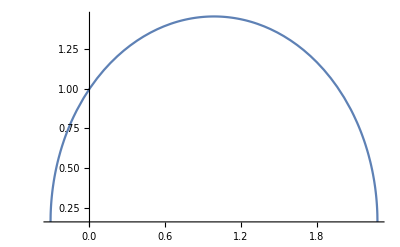

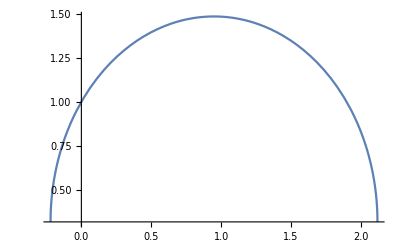

```mathematica
Plot[
UpperHemisphereEquations[[1]],
{
x, 
-ConstructedCircleRadii[[1]] + CircleCPoints[[1,1]],
ConstructedCircleRadii[[1]] + CircleCPoints[[1,1]]
}
]

Plot[
UpperHemisphereEquations[[2]],
{
x, 
-ConstructedCircleRadii[[2]] + CircleCPoints[[2,1]],
ConstructedCircleRadii[[2]] + CircleCPoints[[2,1]]
}
]
```

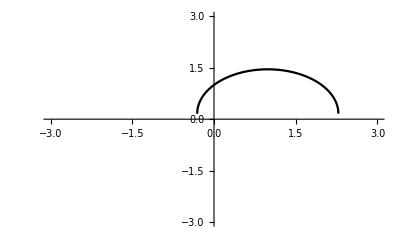
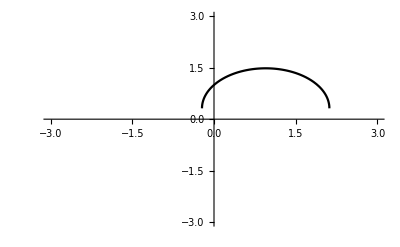
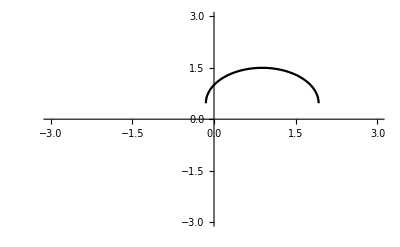
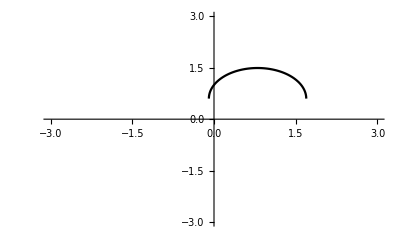
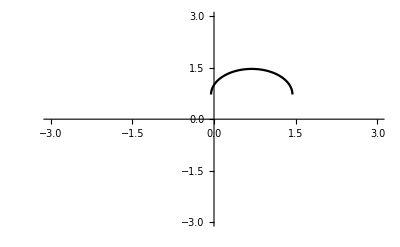
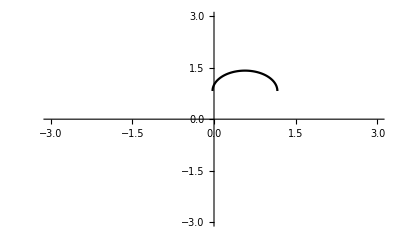
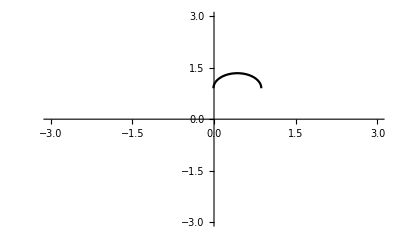
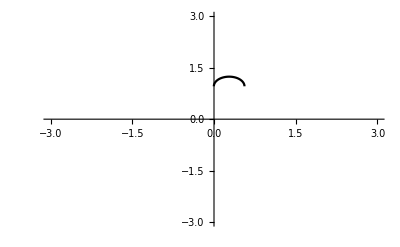

```mathematica
UpperHemispherePlots = Table[
Plot[
UpperHemisphereEquations[[i]],
{
x, 
-ConstructedCircleRadii[[i]] + CircleCPoints[[i,1]],
ConstructedCircleRadii[[i]] + CircleCPoints[[i,1]]
},
PlotStyle -> Black,
PlotRange -> {{-3,3},{-3,3}}
],
{i, Length[ConstructedCircleRadii]}
]
```

Construct the equations for the lower hemisphere of each circle:

Recalling that each circle satisfies:

r^2=(x-CircleCPoints[[i,1]])^2+ (y-CircleCPoints[[i,2]])^2,     (1)

one rearranges to solve for y: 

r^2 - (x-CircleCPoints[[i,1]])^2 = (y-CircleCPoints[[i,2]])^2.     (2)

Taking square roots of each side, and, this time, taking the negative root of the right hand side,  provides:

.03√(.16 r^2-(x-CircleCPoints[[i,1]])^2) = - (y-CircleCPoints[[i,2]]),     (5)

and solving for y gives:

y = CircleCPoints[[i,2]] - √(.16 r^2-(x-CircleCPoints[[i,1]])^2).    (6)

```mathematica
LowerHemisphereEquations = Table[
CircleCPoints[[i,2]] - 
Sqrt[
ConstructedCircleRadii[[i]]^2 - 
(x - CircleCPoints[[i,1]])^2
],
{i, Length[CircleCPoints]}
];
```

Plot each lower hemisphere equation:

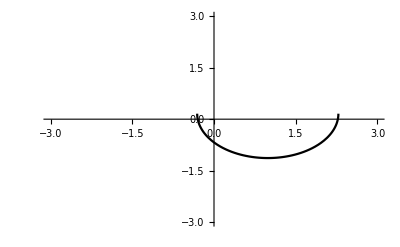
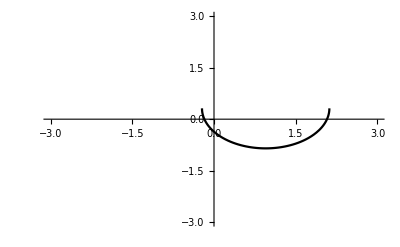
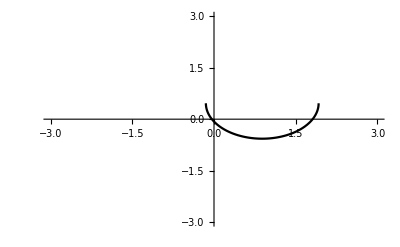
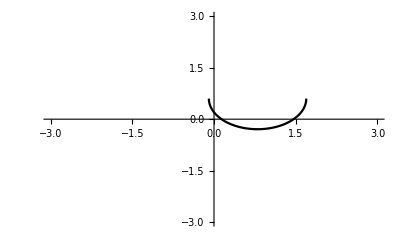
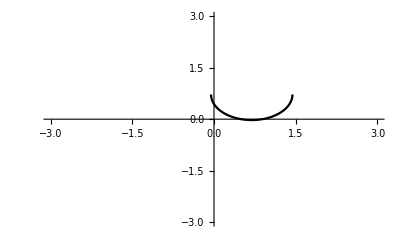
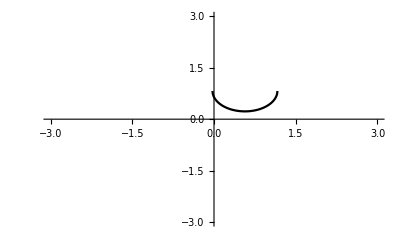
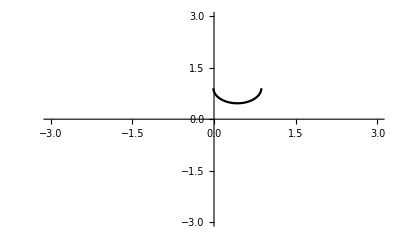
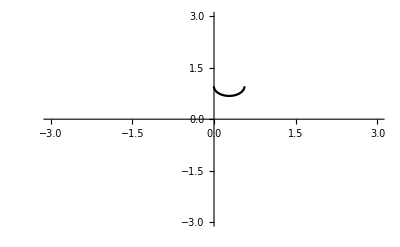

```mathematica
LowerHemispherePlots = Table[
Plot[
LowerHemisphereEquations[[i]],
{
x, 
-ConstructedCircleRadii[[i]] + CircleCPoints[[i,1]],
ConstructedCircleRadii[[i]] + CircleCPoints[[i,1]]
},
PlotStyle -> Black,
PlotRange -> {{-3,3},{-3,3}}
],
{i, Length[ConstructedCircleRadii]}
]
```

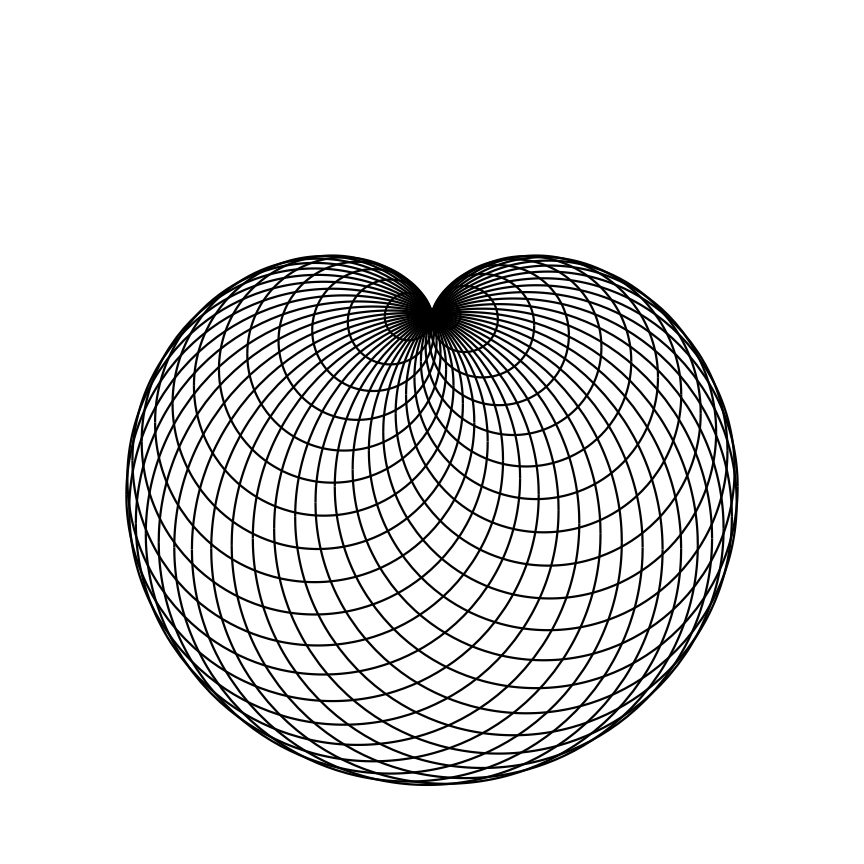

```mathematica
ConstructedCirclePlots = 
Table[
Show[
UpperHemispherePlots[[i]],
LowerHemispherePlots[[i]],
AspectRatio -> 1
],
{i, Length[UpperHemispherePlots]}
];

CardiodPlot = Show[
Table[
ConstructedCirclePlots[[i]],
{i, Length[ConstructedCirclePlots]}
],
Axes -> False,
ImageSize -> {12 72, 12 72}
]
```

## Lise

## I Cardiod Lise Arc-en-Ciel

## Formula for colour transition?

```mathematica
?Hue
```



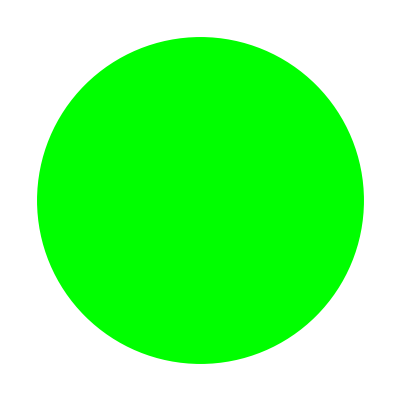

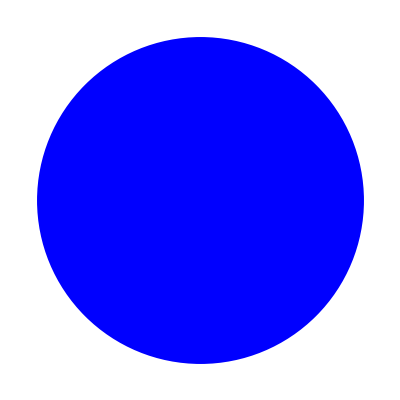

```mathematica
Graphics[{Hue[1],Disk[]}]
Graphics[{Hue[1/3],Disk[]}]
Graphics[{Hue[2/3],Disk[]}]
```

```mathematica
Table[
Graphics[{, Disk[]}],
{i, 6, 1}]
```

{}

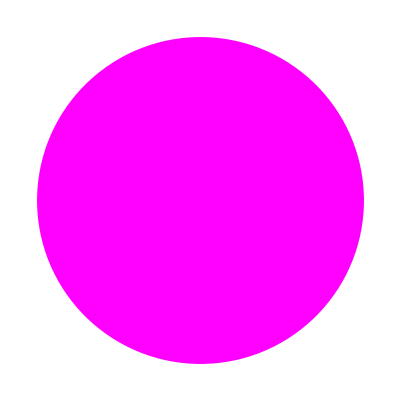
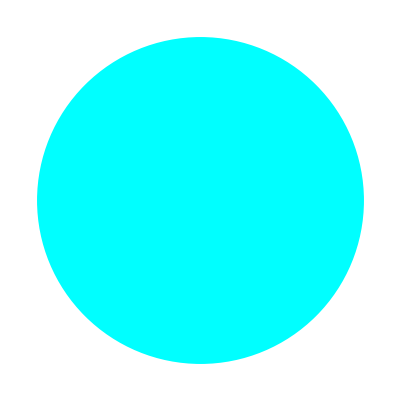
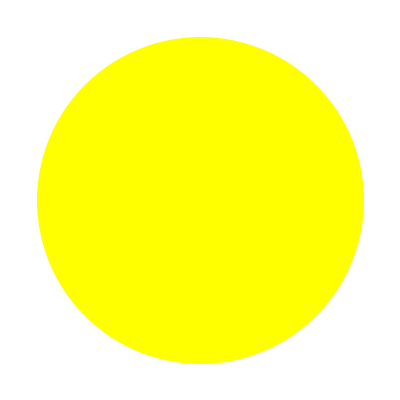
0 | -Graphics-
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4 | -Graphics-
5 | -Graphics-

```mathematica
Table[
{i,
Graphics[{Hue[(6-i)/6],Disk[]}]},
{i, 0, 5}];
%//TableForm
```

```mathematica
Table[
{i,
Graphics[{Hue[0],Disk[]}]},
{i, 0, 5}];
%//TableForm
```

0 | -Graphics-
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4 | -Graphics-
5 | -Graphics-

```mathematica
Table[
{i,
Graphics[{Hue[(6-i)/6],Disk[]}]},
{i, 0, 5, 1/8}];
%//TableForm;
```

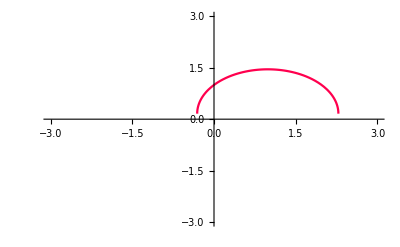
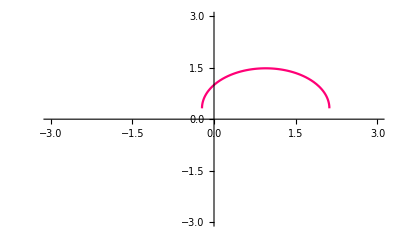
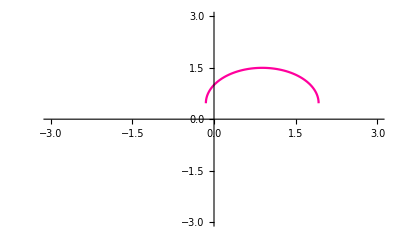
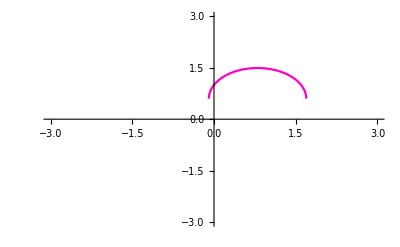
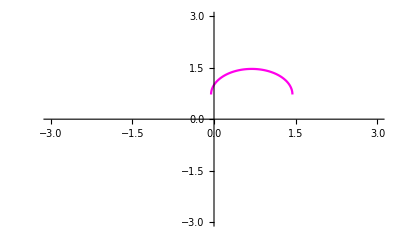
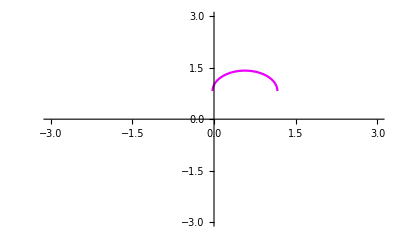
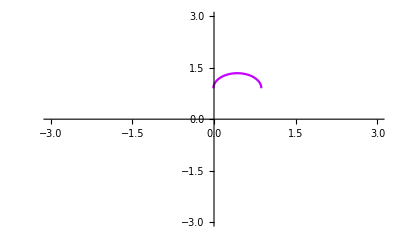
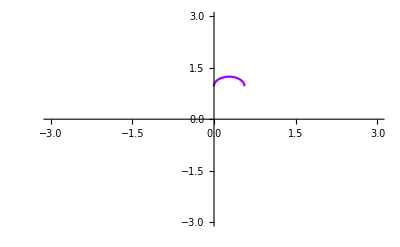
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
UpperHemispherePlots = Table[
Plot[
UpperHemisphereEquations[[i]],
{
x, 
-ConstructedCircleRadii[[i]] + CircleCPoints[[i,1]],
ConstructedCircleRadii[[i]] + CircleCPoints[[i,1]]
},
PlotStyle -> Hue[38/39 -i/39],
PlotRange -> {{-3,3},{-3,3}}
],
{i, Length[ConstructedCircleRadii]}
]

LowerHemispherePlots = Table[
Plot[
LowerHemisphereEquations[[i]],
{
x, 
-ConstructedCircleRadii[[i]] + CircleCPoints[[i,1]],
ConstructedCircleRadii[[i]] + CircleCPoints[[i,1]]
},
PlotStyle -> Hue[38/39 -i/39],
PlotRange -> {{-3,3},{-3,3}}
],
{i, Length[ConstructedCircleRadii]}
]

ConstructedCirclePlots = 
Table[
Show[
UpperHemispherePlots[[i]],
LowerHemispherePlots[[i]],
AspectRatio -> 1
],
{i, Length[UpperHemispherePlots]}
];

CardiodPlot = Show[
Table[
ConstructedCirclePlots[[i]],
{i, Length[ConstructedCirclePlots]}
],
Axes -> False,
ImageSize -> {12 72, 12 72}
]
```